```mathematica
data = {{1,1},{2,2},{3,3},{4,5},{5,7},{6,11},{7,15},{8,22},{9,30},{10,42},{11,56},{12,77},{13,101},{14,135},{15,176},{16,231},{17,297},{18,385},{19,490},{20,627},{21,792},{22,1002},{23,1255},{24,1575},{25,1958},{26,2436},{27,3010},{28,3718},{29,4565},{30,5604},{31,6842},{32,8349},{33,10143},{34,12310},{35,14883},{36,17977},{37,21637},{38,26015},{39,31185},{40,37338},{41,44583},{42,53174},{43,63261},{44,75175},{45,89134},{46,105558},{47,124754},{48,147273},{49,173525},{50,204226},{51,239943},{52,281589},{53,329931},{54,386155},{55,451276},{56,526823},{57,614154},{58,715220},{59,831820},{60,966467},{61,1121505},{62,1300156},{63,1505499},{64,1741630},{65,2012558},{66,2323520},{67,2679689},{68,3087735},{69,3554345},{70,4087968},{71,4697205},{72,5392783},{73,6185689},{74,7089500},{75,8118264},{76,9289091},{77,10619863},{78,12132164},{79,13848650},{80,15796476},{81,18004327},{82,20506255},{83,23338469},{84,26543660},{85,30167357},{86,34262962},{87,38887673},{88,44108109},{89,49995925},{90,56634173},{91,64112359},{92,72533807},{93,82010177},{94,92669720},{95,104651419},{96,118114304},{97,133230930},{98,150198136},{99,169229875},{100,190569292}};
model=a Exp[b x]+c;
fit=FindFit[data,model, {a, {b,1}, {c,First@Mean[data]}}, x]
modelf=Function[{t},Evaluate[model/.fit]]
Plot[modelf[t],{t,0,100}]
```

{a→8.44965×10^-36,b→1.,c→1.28367×10^7}

Function[{t},1.28367×10^7+8.44965×10^-36 ⅇ^(1. x)]

-Graphics-

```mathematica
$GeoLocation=GeoPosition[{22.8885312,-109.9128402}] 
GeoListPlot[GeoNearest["Volcano",Here,10]]
```

GeoPosition[{22.8885,-109.913}]

-Graphics-

```mathematica
Sunset[Here]
Sunrise[Here]
MoonPhase[Now]
```

Sun 12 Jun 2016 20:07GMT-6.

Mon 13 Jun 2016 06:35GMT-6.

0.5688

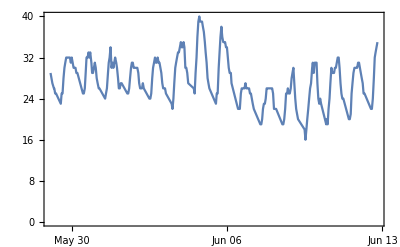

```mathematica
DateListPlot[AirTemperatureData[Here,{DatePlus[Today, -Quantity[2, "Weeks"]],Now}]]
```

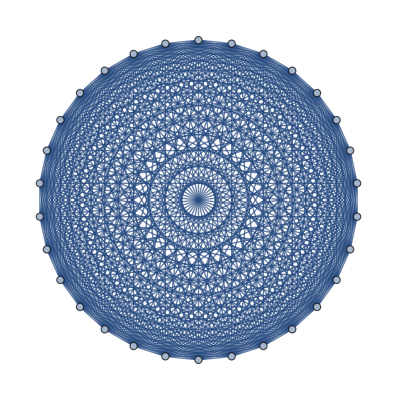

```mathematica
CompleteGraph[30]
```

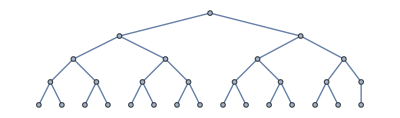

```mathematica
KaryTree[30]
```

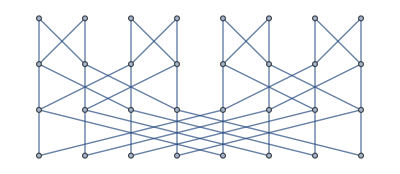

```mathematica
ButterflyGraph[3]
```

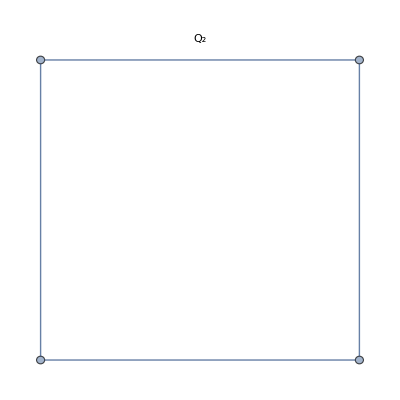
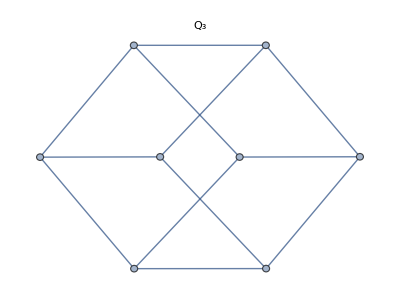
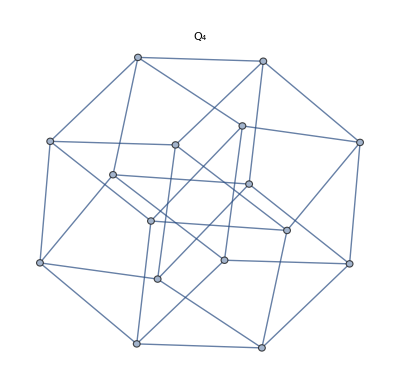

```mathematica
Table[HypercubeGraph[i,PlotLabel->Subscript[Q,i]],{i,2,4}]
```

```mathematica
AdjacencyMatrix[RandomGraph[{5,5}]]
```

SparseArray[<10>, {5, 5}]

```mathematica
NestList[Blur,Rasterize[Style["X",30]],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10]
```

{x,x,x,x,x,x,x,x,x,x,x}

```mathematica
NestList[Rotate[Framed[#],RandomReal[{0,2π}]]&,Rasterize[Style["A"],50],3]
```

{Rasterize[A,50],Rasterize[A,50],Rasterize[A,50],Rasterize[A,50]}

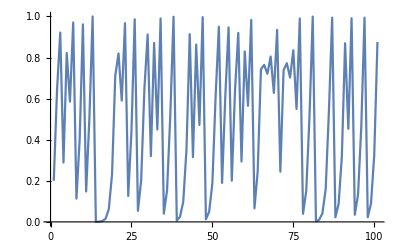

```mathematica
ListLinePlot[NestList[4#(1-#)&,0.2,100]]
```

```mathematica
Nest[1+1/#&,1,30]//N
```

1.61803

```mathematica
NestList[3*#&,1,10] (* powers of three *)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

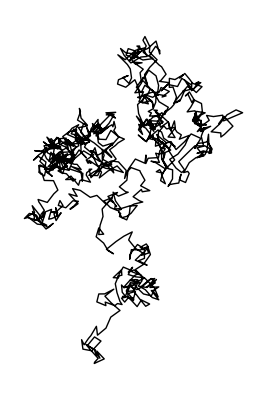

```mathematica
Graphics[Line[NestList[#+RandomReal[{-1,1},2]&,{0,0},1000]]] (*pg160 27.8*)
```

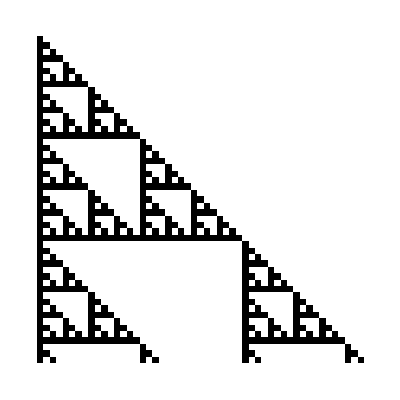

```mathematica
(* Pascal's triangle mod 2 *)
ArrayPlot[NestList[Mod[Join[{0},#]+Join[#,{0}],2]&,{1},50]]
```

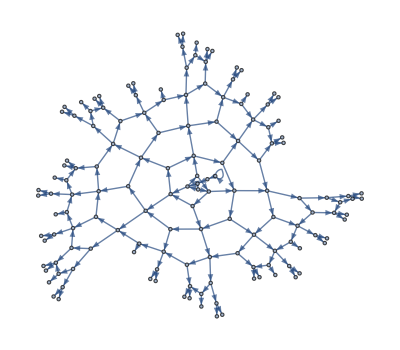

```mathematica
NestGraph[{#+1,2#}&,0,10]
```

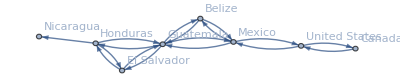

```mathematica
NestGraph[#["BorderingCountries"]&,Entity["Country","UnitedStates"],4,VertexLabels->All]
```

```mathematica
Select[WordList[],StringTake[#,1]==StringTake[StringReverse[#],1]=="p"&]
```

{pap,paperclip,parsnip,partisanship,partnership,pawnshop,payslip,peep,penmanship,pep,pickup,pileup,pimp,pip,plop,plump,polyp,pomp,poop,pop,premiership,prep,primp,professorship,prop,proprietorship,pulp,pump,pup}

```mathematica
If[PrimeQ[#],Style[#,Red],#]&/@Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Select[Array[Prime,100],Last[IntegerDigits[#]]<3&]
```

{2,11,31,41,61,71,101,131,151,181,191,211,241,251,271,281,311,331,401,421,431,461,491,521,541}

```mathematica
Select[RomanNumeral[Range[100]],!MemberQ[Characters[#],"I"]&]
```

{V,X,XV,XX,XXV,XXX,XXXV,XL,XLV,L,LV,LX,LXV,LXX,LXXV,LXXX,LXXXV,XC,XCV,C}

```mathematica
Select[RomanNumeral[Range[1000]],#==StringReverse[#]&]
```

{I,II,III,V,X,XIX,XX,XXX,L,C,CXC,CC,CCC,D,M}

```mathematica
Select[Table[IntegerName[n],{n,100}],First[Characters[#]]==Last[Characters[#]]&]
```

{nineteen,twenty-eight,thirty-eight,eighty-one,eighty-three,eighty-five,eighty-nine,ninety-seven}

```mathematica
Select[TextWords[WikipediaData["words"]],StringLength[#]>15&]
```

{orthographically,multiple-morpheme,Proto-Indo-European}

```mathematica
NestList[If[EvenQ[#],#/2,3#+1]&,1000,200]
```

{1000,500,250,125,376,188,94,47,142,71,214,107,322,161,484,242,121,364,182,91,274,137,412,206,103,310,155,466,233,700,350,175,526,263,790,395,1186,593,1780,890,445,1336,668,334,167,502,251,754,377,1132,566,283,850,425,1276,638,319,958,479,1438,719,2158,1079,3238,1619,4858,2429,7288,3644,1822,911,2734,1367,4102,2051,6154,3077,9232,4616,2308,1154,577,1732,866,433,1300,650,325,976,488,244,122,61,184,92,46,23,70,35,106,53,160,80,40,20,10,5,16,8,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2,1,4,2}

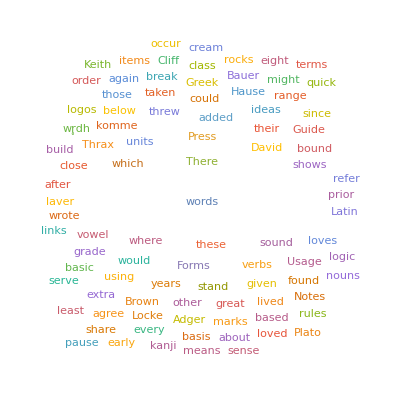

```mathematica
WordCloud[Select[TextWords[WikipediaData["words"]],StringLength[#]==5&]]
```

```mathematica
Select[WordList[],StringLength[#]≥3&&StringTake[#,3]==StringTake[StringReverse[#],3]&&#≠StringReverse[#]&]
```

{despised,detected,detested,drainboard,foolproof,lackadaisical,marjoram,revolver}

```mathematica
Select[WordList[],StringLength[#]==10&&Total[LetterNumber[#]]==100&]
```

{accumulate,alienation,answerable,apoplectic,aquamarine,bewitching,censurable,ceramicist,chastening,chimpanzee,clementine,clinically,collecting,condensate,congenital,conjugated,connivance,declension,deliquesce,demobilize,demodulate,denominate,diagonally,discipline,discommode,egoistical,emasculate,embodiment,emendation,empathetic,fatalistic,fatherhood,geographer,hemoglobin,impugnable,inadequacy,interbreed,leveraging,liberalism,likelihood,martingale,mercantile,meridional,neoclassic,paramecium,plebiscite,potbellied,quadrangle,reciprocal,regimented,reschedule,researcher,scoreboard,septicemia,shibboleth,sleepyhead,stagecraft,stalemated,temperance,thickening,threatened,uncombined,unmodified}

```mathematica
Array[Prime,100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

```mathematica
Array[Prime[#+1]-Prime[#]&,20]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2}

```mathematica
Array[#1+#2&,{10,10}]//Grid
Array[Plus,{10,10}]//Grid
```

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17
9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

```mathematica
FoldList[Times,Range[10]]
FoldList[Times,1,Range[10]]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
FoldList[Times,Array[Prime,10]]
FoldList[Times,1,Array[Prime,10]]
```

{2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

{1,2,6,30,210,2310,30030,510510,9699690,223092870,6469693230}

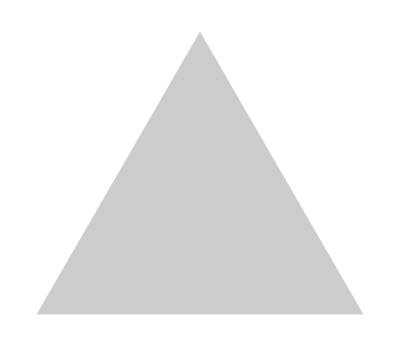
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FoldList[ImageAdd,Table[Graphics[Style[RegularPolygon[n],Opacity[0.2]]],{n,3,8}]]
```


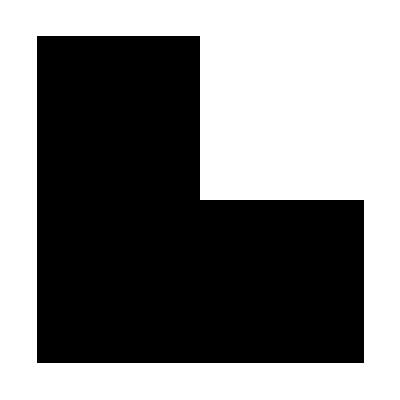
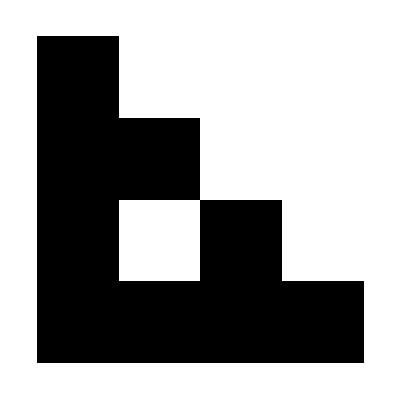

-Graphics-

```mathematica
(* Sierpinski pattern *)
ArrayPlot/@NestList[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},2]
ArrayPlot[Nest[ArrayFlatten[{{#,0},{#,#}}]&,{{1}},8]]
```

```mathematica
Thread[Alphabet["English"]->Range[26]]
```

{a→1,b→2,c→3,d→4,e→5,f→6,g→7,h→8,i→9,j→10,k→11,l→12,m→13,n→14,o→15,p→16,q→17,r→18,s→19,t→20,u→21,v→22,w→23,x→24,y→25,z→26}

```mathematica
Partition[Alphabet["English"],4]//Grid
```

a | b | c | d
e | f | g | h
i | j | k | l
m | n | o | p
q | r | s | t
u | v | w | x

```mathematica
Grid[Partition[Characters[StringTake[WikipediaData["words"],400]],20],Frame->All]
```

I | n |   | l | i | n | g | u | i | s | t | i | c | s | , |   | a |   | w | o
r | d |   | i | s |   | t | h | e |   | s | m | a | l | l | e | s | t |   | e
l | e | m | e | n | t |   | t | h | a | t |   | m | a | y |   | b | e |   | u
t | t | e | r | e | d |   | i | n |   | i | s | o | l | a | t | i | o | n |  
w | i | t | h |   | s | e | m | a | n | t | i | c |   | o | r |   | p | r | a
g | m | a | t | i | c |   | c | o | n | t | e | n | t |   | ( | w | i | t | h
  | l | i | t | e | r | a | l |   | o | r |   | p | r | a | c | t | i | c | a
l |   | m | e | a | n | i | n | g | ) | . |   | T | h | i | s |   | c | o | n
t | r | a | s | t | s |   | d | e | e | p | l | y |   | w | i | t | h |   | a
  | m | o | r | p | h | e | m | e | , |   | w | h | i | c | h |   | i | s |  
t | h | e |   | s | m | a | l | l | e | s | t |   | u | n | i | t |   | o | f
  | m | e | a | n | i | n | g |   | b | u | t |   | w | i | l | l |   | n | o
t |   | n | e | c | e | s | s | a | r | i | l | y |   | s | t | a | n | d |  
o | n |   | i | t | s |   | o | w | n | . |   | A |   | w | o | r | d |   | m
a | y |   | c | o | n | s | i | s | t |   | o | f |   | a |   | s | i | n | g
l | e |   | m | o | r | p | h | e | m | e |   | ( | f | o | r |   | e | x | a
m | p | l | e | : |   | o | h | ! | , |   | r | o | c | k | , |   | r | e | d
, |   | q | u | i | c | k | , |   | r | u | n | , |   | e | x | p | e | c | t
) | , |   | o | r |   | s | e | v | e | r | a | l |   | ( | r | o | c | k | s
, |   | r | e | d | n | e | s | s | , |   | q | u | i | c | k | l | y | , |

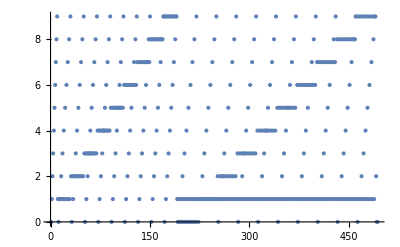

-Graphics-

```mathematica
(* Champernowne *)
ListPlot[Flatten[Table[IntegerDigits[n],{n,0,200}]]]
ListPlot[Flatten[IntegerDigits/@Range[0,200]]]
```

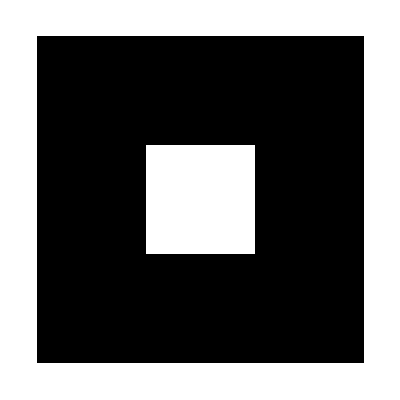
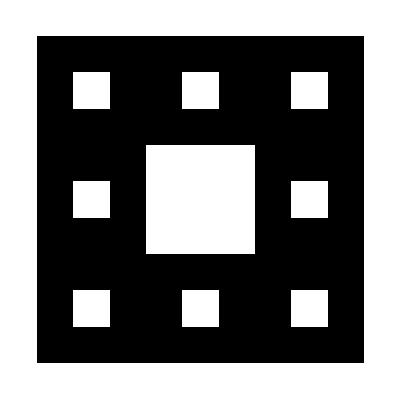
{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

Array[{x,y,√(x^2+y^2)},{x,20},{y,20}]

```mathematica
ArrayPlot/@NestList[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},2]
ArrayPlot[Nest[ArrayFlatten[{{#,#,#},{#,0,#},{#,#,#}}]&,{{1}},4]]
```